# Homework for Chapter 1 - 1

2016314728 정재헌

(#1)  Let  g(x)=1/(ln(x)).             Plot ∫g(x)ⅆx on (0,3).

(#2)  Let  h(x,y)=x/(x^2+y^2). 
Plot the surface represented 
                              by z=h(x,y) with -1≤x≤1 and -1≤y≤1. 
      What is happening at the origin?

#1 풀이_1

```mathematica
Quit
```

1/Log[x]

LogIntegral[x]

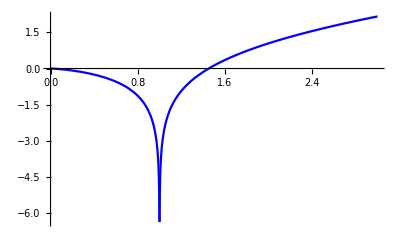

```mathematica
g[x_]=1/Log[x]
f[x_]=Integrate[g[x],x]
Plot[f[x],{x,0,3},PlotStyle->Blue]
```

#1 풀이_2

```mathematica
Quit
```

```mathematica
g[x_] = 1/Log[x]
Plot[Evaluate@Integrate[g[x], x], {x, 0, 3}, PlotStyle -> Blue]
```

1/Log[x]

-Graphics-

#1 풀이_3

```mathematica
Quit
```

```mathematica
g[x_] := 1/Log[x]
```

```mathematica
Plot[Evaluate@Integrate[g[x], x], {x, 0, 3}, PlotStyle -> Blue]
```

-Graphics-

#2 풀이

```mathematica
h[x_,y_]:=x/(x^2+y^2)
```

```mathematica
Plot3D[h[x,y],{x,-1,1},{y,-1,1},PlotStyle->Blue]
```

-Graphics3D-

```mathematica
Gradient[h[0,0]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

∇Indeterminate

즉, h(x,y)=x/(x^2+y^2)그래프는 원점에서 발산한다.

#1 왜 안되는지 모르겠는 경우_1

```mathematica
Quit
```

```mathematica
g[x_] := 1/Log[x]
```

```mathematica
f[x_]:=Integrate[g[x],x]
f[x]
```

LogIntegral[x]

```mathematica
Plot[Evaluate[f[x]], {x, 0, 3}, PlotStyle -> Blue]
```

-Graphics-

#1 왜 안되는지 모르겠는 경우_2

```mathematica
Quit
```

```mathematica
f[x_] := Integrate[1/Log[x],x]
f[x]
```

LogIntegral[x]

```mathematica
Plot[Evaluate[f[x]], {x, 0, 3}, PlotStyle -> Blue]
```

-Graphics-